```mathematica
ClearAll[l]
l[f_]:=Function[Null,f[##],Listable]
```

```mathematica
map={{0,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{0,0,1,0,0},{1,0,0,0,0}};
map2={{0,1,1,1,0},{0,0,1,0,1},{0,0,0,1,1},{1,0,1,1,1},{0,0,1,0,0}};
len=Length[map];
toInt[arr_]:=FromDigits[Reverse@Flatten@Boole@arr,2]
bToInt[arr_]:=FromDigits[Reverse@Flatten@arr,2]
fromInt[int_]:=Partition[Reverse@PadLeft[IntegerDigits[int,2],len^2],len]
update[map_]:=
Module[{padMap,mr,adjCount,a1,a2,m1,m0,ia1,ia2,im1,im0},
padMap=ArrayPad[map,1];
mr=Range[2,len+1];
adjCount=padMap⟦mr,mr+1⟧+padMap⟦mr+1,mr⟧+padMap⟦mr-1,mr⟧+padMap⟦mr,mr-1⟧;
a1=adjCount~l[Equal]~1;
a2=adjCount~l[Equal]~2;
m1=map~l[Equal]~1;
m0=map~l[Equal]~0;
ia1=toInt@a1;ia2=toInt@a2;im1=toInt@m1;im0=toInt@m0;
fromInt[(ia1~BitAnd~im1)~BitOr~(im0~BitAnd~(ia1~BitOr~ia2))]
]
updateInt[int_]:=
Module[{map,padMap,mr,adjCount,a1,a2,m1,m0,ia1,ia2,im1,im0},
map=fromInt[int];
padMap=ArrayPad[map,1];
mr=Range[2,len+1];
adjCount=padMap⟦mr,mr+1⟧+padMap⟦mr+1,mr⟧+padMap⟦mr-1,mr⟧+padMap⟦mr,mr-1⟧;
a1=adjCount~l[Equal]~1;
a2=adjCount~l[Equal]~2;
m1=map~l[Equal]~1;
m0=map~l[Equal]~0;
ia1=toInt@a1;ia2=toInt@a2;im1=toInt@m1;im0=toInt@m0;
(ia1~BitAnd~im1)~BitOr~(im0~BitAnd~(ia1~BitOr~ia2))
]
```

```mathematica
MatrixForm/@NestList[update,map,10];
MatrixForm/@fromInt/@NestList[updateInt,bToInt@map,10];
```

```mathematica
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```

```mathematica
history=NestList[updateInt,bToInt@map,100];
gather=Select[positionDuplicates@history,Length[#]>1&]
minIdx=Min@Flatten@gather;
history[[minIdx]]
```

{{20,78},{21,79},{22,80},{23,81},{24,82},{25,83},{26,84},{27,85},{28,86},{29,87},{30,88},{31,89},{32,90},{33,91},{34,92},{35,93},{36,94},{37,95},{38,96},{39,97},{40,98},{41,99},{42,100},{43,101}}

27562081

```mathematica
(* end part 1; begin part 2 *)
```

```mathematica
updateFromCount[map_,adjCount_]:=
Module[{padMap,mr,a1,a2,m1,m0,ia1,ia2,im1,im0},
padMap=ArrayPad[map,1];
mr=Range[2,len+1];
a1=adjCount~l[Equal]~1;
a2=adjCount~l[Equal]~2;
m1=map~l[Equal]~1;
m0=map~l[Equal]~0;
ia1=toInt@a1;ia2=toInt@a2;im1=toInt@m1;im0=toInt@m0;
fromInt[(ia1~BitAnd~im1)~BitOr~(im0~BitAnd~(ia1~BitOr~ia2))]
]
```

```mathematica
one5=Table[1,{5},{5}];
one5[[3,3]]=0;
centerMask=bToInt@one5
```

33550335

```mathematica
borderSum[map_]:={Sum[map⟦1,i⟧,{i,5}],Sum[map⟦5,i⟧,{i,5}],Sum[map⟦i,1⟧,{i,5}],Sum[map⟦i,5⟧,{i,5}]}
```

```mathematica
inBorder[map_]:={map⟦2,3⟧,map⟦4,3⟧,map⟦3,2⟧,map⟦3,4⟧}
```

```mathematica
inBorder@map
```

{1,1,0,1}

```mathematica
customPadMap[map_,border_]:=Module[{newMap=map},
newMap=ArrayPad[newMap,{{1,0},{0}},border[[1]]];
newMap=ArrayPad[newMap,{{0,1},{0}},border[[2]]];
newMap=ArrayPad[newMap,{{0},{1,0}},border[[3]]];
newMap=ArrayPad[newMap,{{0},{0,1}},border[[4]]];
newMap
]
len=5;
mr=Range[2,len+1];
makeAdjCount[padMap_]:=padMap⟦mr,mr+1⟧+padMap⟦mr+1,mr⟧+padMap⟦mr-1,mr⟧+padMap⟦mr,mr-1⟧;
getNext[adjCount_,map_]:=Module[{a1,a2,m1,m0,ia1,ia2,im1,im0},
a1=adjCount~l[Equal]~1;
a2=adjCount~l[Equal]~2;
m1=map~l[Equal]~1;
m0=map~l[Equal]~0;
ia1=toInt@a1;ia2=toInt@a2;im1=toInt@m1;im0=toInt@m0;
fromInt[((ia1~BitAnd~im1)~BitOr~(im0~BitAnd~(ia1~BitOr~ia2)))~BitAnd~centerMask]
]
```

```mathematica
updateList[mapList_]:=Module[{newMapList,outBorders,inBorders,paddedMaps,adjCounts,extOldMaps,i1,i2},
(* first figure out the levels that already exist; then figure out if need to make new levels *)
outBorders=borderSum/@mapList;
inBorders={{0,0,0,0}}~Join~(inBorder/@mapList);
(* 1st element is outermost, nth element is innermost *)
extOldMaps=mapList~Join~{Table[0,{5},{5}]};
paddedMaps=Table[customPadMap[extOldMaps⟦k⟧,inBorders⟦k⟧],{k,1+Length@mapList}];
adjCounts={Table[0,{5},{5}]}~Join~(makeAdjCount/@paddedMaps);(* 1st is one level outer than outermost, last is one level inner than innermost *)
Do[
adjCounts⟦n⟧⟦2,3⟧+=outBorders⟦n⟧⟦1⟧;
adjCounts⟦n⟧⟦4,3⟧+=outBorders⟦n⟧⟦2⟧;
adjCounts⟦n⟧⟦3,2⟧+=outBorders⟦n⟧⟦3⟧;
adjCounts⟦n⟧⟦3,4⟧+=outBorders⟦n⟧⟦4⟧,
{n,1,Length@mapList}
];
extOldMaps={Table[0,{5},{5}]}~Join~extOldMaps;
newMapList=Table[getNext[adjCounts[[k]],extOldMaps[[k]]],{k,1,2+Length@mapList}];
i1=If[Total@Flatten@newMapList⟦1⟧>0,1,2];
i2=If[Total@Flatten@newMapList⟦2+Length@mapList⟧>0,2+Length@mapList,1+Length@mapList];
newMapList⟦i1;;i2⟧
]
```

```mathematica
borderSum/@{map,map}
```

{{3,1,1,3},{3,1,1,3}}

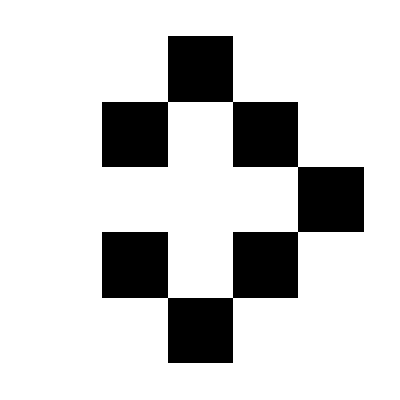
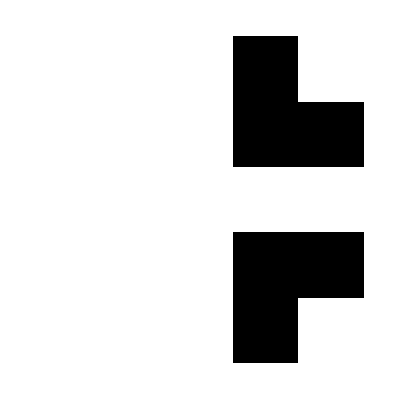
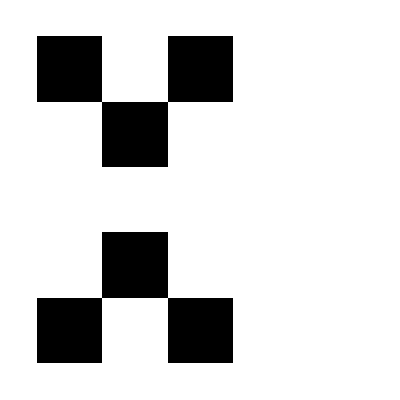
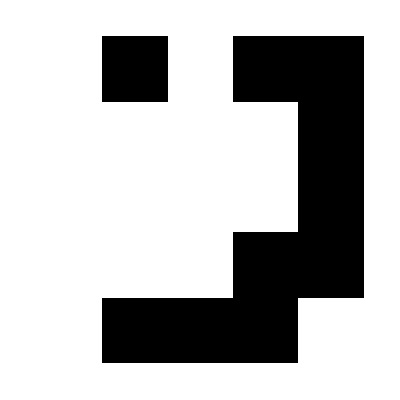
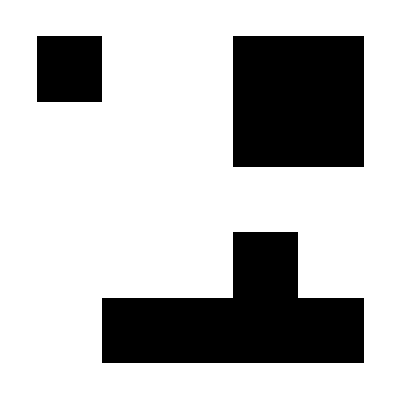
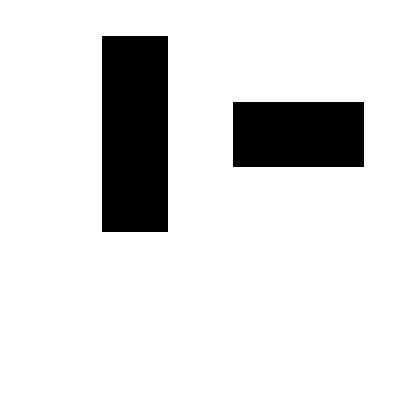
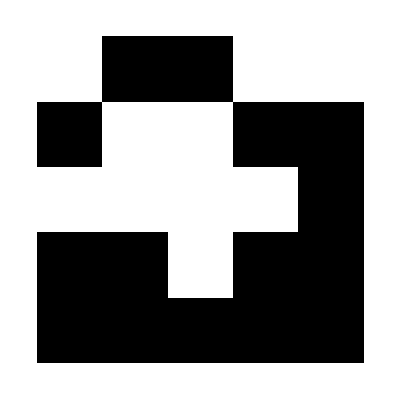
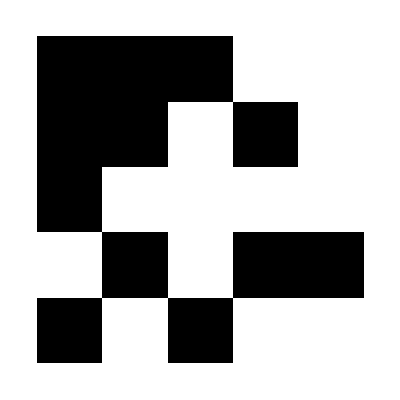

```mathematica
ArrayPlot/@Nest[updateList,{map},10]
```

```mathematica
Total@Flatten@Nest[updateList,{map2},200]
```

1893